# Контролна работа №2 III вариант, задача 2 Фак. №2001261051

## Дадена е началната задача за ОДУ: y’ = y - (2 + a)sinx, y(b) = a + b, x ϵ [b; b + 0.5]

### a) Да се намери точното решение на задачата

Търсим точно решение :

```mathematica
Clear[x,y]
DSolve[{y'[x]==y[x]-(2+5)Sin[x], y[1]==6}, y[x],x]
```

{{y[x]→(12 ⅇ^x-7 ⅇ^x Cos[1]+7 ⅇ Cos[x]-7 ⅇ^x Sin[1]+7 ⅇ Sin[x])/(2 ⅇ)}}

Визуализация на точно решение:

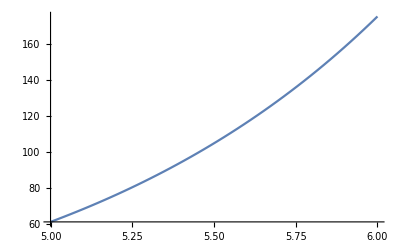

```mathematica
yt[x_]:=(12 ⅇ^x-7 ⅇ^x Cos[1]+7 ⅇ Cos[x]-7 ⅇ^x Sin[1]+7 ⅇ Sin[x])/(2 ⅇ)
Plot[yt[x], {x, a,b}]
```

### б) По метод на Рунге-Кута (1/2, 1/2) да се реши приближено задачата със стъпка (h) 0.02. Запишете резултатите в таблица. Сравнете с точното решение

Мрежата е с n = 25. и стъпка h = 0.02

Теоретичната локална  грешка е 8.×10^-6

Теоретичната глобална грешка е 0.0004

i = 0, x_i = 1., y_i = 6., k1 = 0.00219406, k2 = 0.00146548, y_точно = 6., истинска грешка = 8.88178×10^-16

i = 1, x_i = 1.02, y_i = 6.00147, k1 = 0.000734187, k2 = 0.000014793, y_точно = 6.00146, истинска грешка = 2.90567×10^-6

i = 2, x_i = 1.04, y_i = 6.00148, k1 = -0.000706986, k2 = -0.00141672, y_точно = 6.00147, истинска грешка = 5.78407×10^-6

i = 3, x_i = 1.06, y_i = 6.00006, k1 = -0.0021285, k2 = -0.00282808, y_точно = 6.00005, истинска грешка = 8.63225×10^-6

i = 4, x_i = 1.08, y_i = 5.99724, k1 = -0.00352938, k2 = -0.00421835, y_точно = 5.99722, истинска грешка = 0.0000114472

i = 5, x_i = 1.1, y_i = 5.99302, k1 = -0.00490869, k2 = -0.00558656, y_точно = 5.993, истинска грешка = 0.0000142259

i = 6, x_i = 1.12, y_i = 5.98743, k1 = -0.00626545, k2 = -0.00693175, y_точно = 5.98741, истинска грешка = 0.0000169652

i = 7, x_i = 1.14, y_i = 5.9805, k1 = -0.00759871, k2 = -0.00825296, y_точно = 5.98048, истинска грешка = 0.0000196619

i = 8, x_i = 1.16, y_i = 5.97225, k1 = -0.00890752, k2 = -0.00954924, y_точно = 5.97222, истинска грешка = 0.0000223129

i = 9, x_i = 1.18, y_i = 5.9627, k1 = -0.0101909, k2 = -0.0108196, y_точно = 5.96267, истинска грешка = 0.0000249149

i = 10, x_i = 1.2, y_i = 5.95188, k1 = -0.0114479, k2 = -0.0120632, y_точно = 5.95185, истинска грешка = 0.0000274646

i = 11, x_i = 1.22, y_i = 5.93981, k1 = -0.0126776, k2 = -0.0132789, y_точно = 5.93978, истинска грешка = 0.0000299586

i = 12, x_i = 1.24, y_i = 5.92653, k1 = -0.0138791, k2 = -0.0144659, y_точно = 5.9265, истинска грешка = 0.0000323935

i = 13, x_i = 1.26, y_i = 5.91207, k1 = -0.0150513, k2 = -0.0156233, y_точно = 5.91203, истинска грешка = 0.0000347658

i = 14, x_i = 1.28, y_i = 5.89645, k1 = -0.0161933, k2 = -0.0167499, y_точно = 5.89641, истинска грешка = 0.000037072

i = 15, x_i = 1.3, y_i = 5.8797, k1 = -0.0173042, k2 = -0.017845, y_точно = 5.87966, истинска грешка = 0.0000393084

i = 16, x_i = 1.32, y_i = 5.86185, k1 = -0.0183831, k2 = -0.0189076, y_точно = 5.86181, истинска грешка = 0.0000414715

i = 17, x_i = 1.34, y_i = 5.84294, k1 = -0.019429, k2 = -0.0199367, y_точно = 5.8429, истинска грешка = 0.0000435575

i = 18, x_i = 1.36, y_i = 5.82301, k1 = -0.0204409, k2 = -0.0209314, y_точно = 5.82296, истинска грешка = 0.0000455626

i = 19, x_i = 1.38, y_i = 5.80208, k1 = -0.021418, k2 = -0.0218908, y_точно = 5.80203, истинска грешка = 0.000047483

i = 20, x_i = 1.4, y_i = 5.78018, k1 = -0.0223593, k2 = -0.0228139, y_точно = 5.78013, истинска грешка = 0.0000493148

i = 21, x_i = 1.42, y_i = 5.75737, k1 = -0.0232638, k2 = -0.0236999, y_точно = 5.75732, истинска грешка = 0.000051054

i = 22, x_i = 1.44, y_i = 5.73367, k1 = -0.0241308, k2 = -0.0245477, y_точно = 5.73362, истинска грешка = 0.0000526966

i = 23, x_i = 1.46, y_i = 5.70912, k1 = -0.0249591, k2 = -0.0253565, y_точно = 5.70907, истинска грешка = 0.0000542386

i = 24, x_i = 1.48, y_i = 5.68377, k1 = -0.025748, k2 = -0.0261254, y_точно = 5.68371, истинска грешка = 0.0000556756

i = 25, x_i = 1.5, y_i = 5.65764, k1 = -0.0264965, k2 = -0.0268535, y_точно = 5.65758, истинска грешка = 0.0000570036

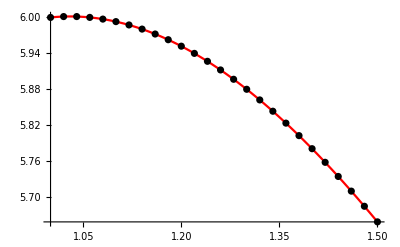

```mathematica
(*Въвеждаме условието на задачата*)
a = 1.; b = 1.5;
x = a;
y = 6.;
points = {{x,y}};
f[x_,y_]:=y-(2+5)Sin[x]

(*Точно решение*)
yt[x_]:=(12 ⅇ^x-7 ⅇ^x Cos[1]+7 ⅇ Cos[x]-7 ⅇ^x Sin[1]+7 ⅇ Sin[x])/(2 ⅇ)

(*Съставяме мрежата*)
h = 0.02; n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
k1=h*f[x,y];
k2=h*f[x+h/2,y+k1/2];
Print["i = ", i, ", x_i = ",x, ", y_i = ",y, ", k1 = ",k1,", k2 = ",k2,", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y+k2;
x=x+h;
AppendTo[points,{x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

### в) Каква е теоретичната грешка на полученото приближено решение?

```mathematica
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Теоретичната локална  грешка е 8.×10^-6

Теоретичната глобална грешка е 0.0004

### г) Каква би била точността при използване на метода на Ойлер за поставената задача със същата стъпка? Направете сравнение между двата метода.

Мрежата е с n = 25. и стъпка h = 0.02

Теоретичната локална грешка  е 0.0004

Теоретичната глобална грешка е 0.02

i = 0, x_i = 1., y_i = 6., f_i = 0.109703, y_точно = 6., истинска грешка = 8.88178×10^-16

i = 1, x_i = 1.02, y_i = 6.00219, f_i = 0.0374379, y_точно = 6.00146, истинска грешка = 0.000731485

i = 2, x_i = 1.04, y_i = 6.00294, f_i = -0.0338868, y_точно = 6.00147, истинска грешка = 0.00146833

i = 3, x_i = 1.06, y_i = 6.00227, f_i = -0.104223, y_точно = 6.00005, истинска грешка = 0.00221016

i = 4, x_i = 1.08, y_i = 6.00018, f_i = -0.173524, y_точно = 5.99722, истинска грешка = 0.00295659

i = 5, x_i = 1.1, y_i = 5.99671, f_i = -0.241741, y_точно = 5.993, истинска грешка = 0.00370724

i = 6, x_i = 1.12, y_i = 5.99188, f_i = -0.308828, y_точно = 5.98741, истинска грешка = 0.00446171

i = 7, x_i = 1.14, y_i = 5.9857, f_i = -0.374736, y_точно = 5.98048, истинска грешка = 0.0052196

i = 8, x_i = 1.16, y_i = 5.9782, f_i = -0.439418, y_точно = 5.97222, истинска грешка = 0.0059805

i = 9, x_i = 1.18, y_i = 5.96942, f_i = -0.502826, y_точно = 5.96267, истинска грешка = 0.00674399

i = 10, x_i = 1.2, y_i = 5.95936, f_i = -0.564914, y_точно = 5.95185, истинска грешка = 0.00750965

i = 11, x_i = 1.22, y_i = 5.94806, f_i = -0.625635, y_точно = 5.93978, истинска грешка = 0.00827703

i = 12, x_i = 1.24, y_i = 5.93555, f_i = -0.68494, y_точно = 5.9265, истинска грешка = 0.00904571

i = 13, x_i = 1.26, y_i = 5.92185, f_i = -0.742783, y_точно = 5.91203, истинска грешка = 0.00981522

i = 14, x_i = 1.28, y_i = 5.90699, f_i = -0.799117, y_точно = 5.89641, истинска грешка = 0.0105851

i = 15, x_i = 1.3, y_i = 5.89101, f_i = -0.853896, y_точно = 5.87966, истинска грешка = 0.0113549

i = 16, x_i = 1.32, y_i = 5.87393, f_i = -0.907072, y_точно = 5.86181, истинска грешка = 0.0121242

i = 17, x_i = 1.34, y_i = 5.85579, f_i = -0.9586, y_точно = 5.8429, истинска грешка = 0.0128924

i = 18, x_i = 1.36, y_i = 5.83662, f_i = -1.00843, y_точно = 5.82296, истинска грешка = 0.0136591

i = 19, x_i = 1.38, y_i = 5.81645, f_i = -1.05652, y_точно = 5.80203, истинска грешка = 0.0144238

i = 20, x_i = 1.4, y_i = 5.79532, f_i = -1.10283, y_точно = 5.78013, истинска грешка = 0.015186

i = 21, x_i = 1.42, y_i = 5.77326, f_i = -1.1473, y_точно = 5.75732, истинска грешка = 0.0159451

i = 22, x_i = 1.44, y_i = 5.75032, f_i = -1.18989, y_точно = 5.73362, истинска грешка = 0.0167007

i = 23, x_i = 1.46, y_i = 5.72652, f_i = -1.23056, y_точно = 5.70907, истинска грешка = 0.0174521

i = 24, x_i = 1.48, y_i = 5.70191, f_i = -1.26926, y_точно = 5.68371, истинска грешка = 0.0181989

i = 25, x_i = 1.5, y_i = 5.67652, f_i = -1.30594, y_точно = 5.65758, истинска грешка = 0.0189406

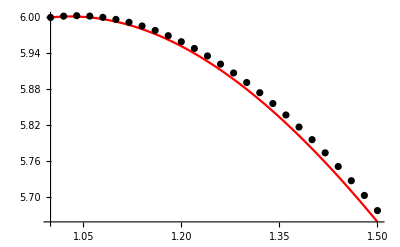

```mathematica
(*Въвеждаме условието на задачата*)
a = 1.; b = 1.5;
x = a;
y = 6.;
points = {{x,y}};
f[x_,y_]:=y-(2+5)Sin[x]

(*Точно решение*)
yt[x_]:=(12 ⅇ^x-7 ⅇ^x Cos[1]+7 ⅇ Cos[x]-7 ⅇ^x Sin[1]+7 ⅇ Sin[x])/(2 ⅇ)

(*Съставяме мрежата*)
h = 0.02; n = (b-a)/h;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]

(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална грешка  е ", h^2]
Print["Теоретичната глобална грешка е ", h]

(*Намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i  <= n, i++,
Print["i = ", i, ", x_i = ", x, ", y_i = ", y, ", f_i = ", f[x,y] , ", y_(:0442:043e:0447:043d:043e) = ", yt[x], ", истинска грешка = ", Abs[y-yt[x]]];
y = y + h*f[x,y];
x = x + h;
AppendTo[points, {x,y}]
]

(*Визуализация на резултатите*)
gryt = Plot[yt[x], {x, a, b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt, grp]
```